```mathematica
{NotebookFileName[],DateString[]}
```

{D:\WSL\morpheus\worm2\worm2.nb,Fri 5 Mar 2021 11:42:12}

## Setup

```mathematica
Needs["Developer`"]
```

```mathematica
$HistoryLength=5
```

5

```mathematica
curDir=FileNameDrop[NotebookFileName[]]
```

D:\WSL\morpheus\worm2

```mathematica
modelName=FileNameTake[curDir,-1]
```

worm2

```mathematica
logFile="logger.csv"
```

logger.csv

## Sweep 7

```mathematica
sweep=7
```

7

```mathematica
sweepDir=FileNameJoin[{curDir,modelName<>"_sweep_"<>ToString[sweep]}]
```

D:\WSL\morpheus\worm2\worm2_sweep_7

```mathematica
sweeps7=FileNames[modelName<>"*",sweepDir]
```

{D:\WSL\morpheus\worm2\worm2_sweep_7\worm2_76,D:\WSL\morpheus\worm2\worm2_sweep_7\worm2_77,D:\WSL\morpheus\worm2\worm2_sweep_7\worm2_78,D:\WSL\morpheus\worm2\worm2_sweep_7\worm2_79,D:\WSL\morpheus\worm2\worm2_sweep_7\worm2_80,D:\WSL\morpheus\worm2\worm2_sweep_7\worm2_81,D:\WSL\morpheus\worm2\worm2_sweep_7\worm2_82,D:\WSL\morpheus\worm2\worm2_sweep_7\worm2_83,D:\WSL\morpheus\worm2\worm2_sweep_7\worm2_84,D:\WSL\morpheus\worm2\worm2_sweep_7\worm2_85}

```mathematica
sweep7a=Import[
FileNameJoin[{sweeps7⟦1⟧,logFile}],
{"CSV","Dataset"}
,HeaderLines->1
]
```

```mathematica
sweep7a⟦1⟧["MKtemp"]
```

0.2

```mathematica
sweep7a⟦1⟧//Keys
```

```mathematica
sweep7a[GroupBy["time"]]⟦-1⟧
```

```mathematica
sweep7a[GroupBy["time"]]⟦-1⟧[StandardDeviation]
```

```mathematica
estimateDiffusion[
sweepDir_String,
logName_:logFile
]:=Module[{sweepds,tfinal,temp,σx,σy},
sweepds=Import[
FileNameJoin[{sweepDir,logName}],
{"CSV","Dataset"}
,HeaderLines->1
];
sweepds=sweepds[GroupBy["time"]]⟦-1⟧;
temp=sweepds⟦1⟧["MKtemp"];
tfinal=sweepds⟦1⟧["time"];
{σx,σy}=sweepds[All,{"delta_r.x","delta_r.y"}][StandardDeviation]/@{"delta_r.x","delta_r.y"};
{temp,tfinal,(σx^2+σy^2)/(4tfinal)}
]
```

```mathematica
estimateDiffusion[sweeps7⟦1⟧]
```

{0.2,10000,0.0161604}

```mathematica
estimateDiffusion/@sweeps7
```

{{0.2,10000,0.0161604},{0.4,10000,0.0665741},{0.6,10000,0.111487},{0.8,10000,0.116239},{1,10000,0.144375},{1.2,10000,0.151445},{1.4,10000,0.155824},{1.6,10000,0.172607},{1.8,10000,0.190152},{2,10000,0.176751}}

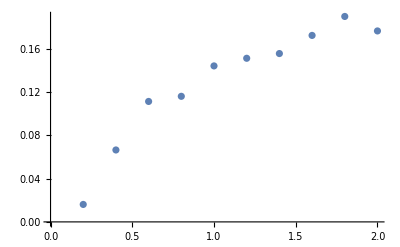

```mathematica
ListPlot[(estimateDiffusion/@sweeps7)⟦;;,{1,3}⟧
]
```

## Sweep 8

```mathematica
sweep=8
```

8

```mathematica
sweepDir=FileNameJoin[{curDir,modelName<>"_sweep_"<>ToString[sweep]}]
```

D:\WSL\morpheus\worm2\worm2_sweep_8

```mathematica
sweeps8=FileNames[modelName<>"*",sweepDir]
```

{D:\WSL\morpheus\worm2\worm2_sweep_8\worm2_86,D:\WSL\morpheus\worm2\worm2_sweep_8\worm2_87,D:\WSL\morpheus\worm2\worm2_sweep_8\worm2_88,D:\WSL\morpheus\worm2\worm2_sweep_8\worm2_89,D:\WSL\morpheus\worm2\worm2_sweep_8\worm2_90,D:\WSL\morpheus\worm2\worm2_sweep_8\worm2_91,D:\WSL\morpheus\worm2\worm2_sweep_8\worm2_92,D:\WSL\morpheus\worm2\worm2_sweep_8\worm2_93,D:\WSL\morpheus\worm2\worm2_sweep_8\worm2_94,D:\WSL\morpheus\worm2\worm2_sweep_8\worm2_95}

```mathematica
estimateDiffusion/@sweeps8
```

{{1,10000,0.144375},{2,10000,0.176751},{3,10000,0.196309},{4,10000,0.192582},{5,10000,0.226427},{6,10000,0.23304},{7,10000,0.1751},{8,10000,0.211865},{9,10000,0.247846},{10,10000,0.20049}}

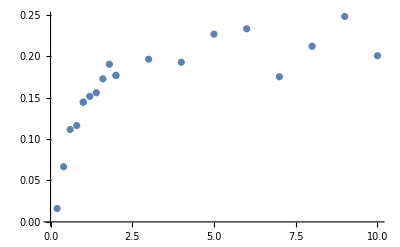

```mathematica
ListPlot[Join[
estimateDiffusion/@sweeps7,estimateDiffusion/@sweeps8
]⟦;;,{1,3}⟧
]
```